# Red neuronal artificial

## Introducción

Una red neuronal artificial es un modelo de ajuste basado en el sistema nervioso donde la entrada es un vector x ∈ ℝ^N, y se desea mapear a f(x) ∈ ℝ^M, donde N y M son enteros arbitrariamente grandes. x es el estímulo de entrada que recibe la red, y f(x) es el estímulo de salida. Este modelo está basado en una estructura de capas, donde el estímulo se recibe en la capa de entrada, y el resultado se obtiene en la capa de salida. Cada neurona está interconectada con las demás de la siguiente capa. 
-Graphics-
La fuerza de la conexión entre neuronas está dada por el peso w de la conexión y el bias b. De manera que el resultado de una neurona al procesar la señal es f(∑_i w_ij x_i + b_i), donde f es una función de activación, w_ij es el peso de la conexión de la neurona i con la neurona j, donde i y j están en diferentes capas, y b_i es el bias de la neurona i. Una manera de realizar el conteo de todas las capas que existen en la red neuronal es agregando un tercer índice k, que indique entre qué capas está,  f(∑_i w_ij^k x_i^k + b_i^k).
Un tipo muy usado de neuronas artficiciales es la neurona sigmoide, donde la señal de salida de una neurona en función de su entrada se calcula a través de la función sigmoide.
-Graphics-
La función sigmoide tiene la particularidad de que devuelve siempre un valor entre 0 y 1.

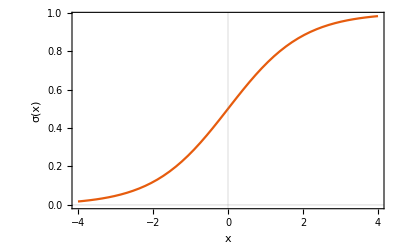

```mathematica
Plot[LogisticSigmoid[x],{x,-4,4}, FrameLabel->{"x","σ(x)"},PlotTheme->"Scientific"]
```

La activación de la neurona está dada por
σ(z) = 1/(1+exp(-∑_j w_ji x_j-b)). 

Por la estructura matemática de este modelo conviene representar todo en forma matricial, de manera que la notación se reduce a
σ(z) = σ(w·x + b).

La propagación hacia delante (feedforward) consiste entonces en aplicar sucesivamente esta función,
x^2 = σ(w^1·x^1+b^1),
x^3 = σ(w^2·x^2+b^2),
⋮
x^N = σ(w^(N-1)·x^(N-1)+b^(N-1)).

La red neuronal trabaja propagando hacia delante la señal inicial mediante la función de activación hasta que se llega a la capa de salida. Si se inicia con una matriz de pesos y bias aleatorios la red neuronal inicialmente no producirá los resultados deseados. La manera en la que podemos determinar qué tan lejos estamos de los resultados es mediante una función de costo
C(w, b) = 1/(2n)∑_x (|y(x)-a|)^2, 

donde w y b son los pesos y los biases.
Con esto se puede conocer cuánto se deben cambiar w y b para que el costo sea menor, es decir, estar más cerca del resultado correcto.
w_k→ w'_k= w_k- η (∂C)/(∂ w_k),
b_l→ b'_l= b_l- η (∂C)/(∂ b_l).

Al aplicar sucesivamente este procedimiento se espera llegar a un resultado cada vez más cercano al correcto. El algoritmo para calcular las derivadas parciales (∂C)/(∂ w_k) y  (∂C)/(∂ b_l) secomoce como el algoritmo de retropropagación. Este consiste en:

Entrada: Establecer la activación a^1 correspondiente para la capa de entrada.

Feedforward: Para cada l = 2,3,…,L se calcula z^l = w^l a^(l-1)+b^l y a^l = σ(z^l).

Error de salida δ^L: Se calcula el vector δ^L = ∇_a C ⊙ σ'(z^L).

Retropropagar el error: Para cada l=L-1, L-2,…,2 calcular δ^l = ((w^(l+1))^T δ^(l+1))⊙σ'(z^l).

Resultado: La derivada parcial de la función de costo es (∂C)/(∂ (w^l)_jk) = a_k^(l-1)δ_j^l y (∂C)/(∂ b_j^l) = δ_j^l.

## Implementación

Esta implementación se basa en la que se ofrece en el libro: http://neuralnetworksanddeeplearning.com.

```mathematica
(* Se inician las matrices con valores aleatorios. *)
Initialize[asizes_] :=(
layers = Length[asizes];
sizes = asizes;
bshape = Transpose[{sizes[[2;;]],Table[1,{Length[sizes]-1}]}];
wshape = Transpose[{sizes[[2;;]],sizes[[;;-2]]}];
biases =  Table[RandomReal[{0,1},i],{i,bshape}];
weights =Table[RandomReal[{0,1},i],{i,wshape}];
);

Cost[y_,a_]:= 1/2(y-a)^2;
CostPrime[y_,a_]:=D[Cost[yt,at],at] /. {yt->y,at->a};
Sigmoid[x_]:=LogisticSigmoid[x];
SigmoidPrime[x_] := D[LogisticSigmoid[xt],xt] /. xt -> x;

(* Para formatear el vector de entrada al estilo de matriz de Mathematica. *)
FormatA[array_] := Table[{i},{i,array}];

FeedForward[alist_] := Module[{bwlength, a,w, b},
bwlength = Length[weights];
a = alist;
Do[
w = weights[[i]];
b = biases[[i]];
a = LogisticSigmoid[w.a + b];
,{i,1,bwlength}
];
Return[a];
];

Backprop[x_,y_]:=Module[{nablaB, nablaW, activation,activations,z,zs,bwlength,w,b,delta},
nablaB= Table[ConstantArray[0,i],{i,bshape}];
nablaW= Table[ConstantArray[0,i],{i,wshape}];
activation =FormatA[x];
activations = {FormatA[x]};
zs = {};
bwlength = Length[weights];

(* Calcula todos los feedforwards. *)
Do[
w = weights[[i]];
b = biases[[i]];
z = w.activation + b;
activation =Sigmoid[z];
AppendTo[zs,z];
AppendTo[activations, activation];
,{i,1,bwlength}
];

(* Calcula los errores de salida y retropropaga. *)
delta = CostPrime[y,activations[[-1]]] * SigmoidPrime[zs[[-1]]];
nablaB[[-1]] = delta;
nablaW[[-1]] = delta.Transpose[activations[[-2]]];

Do[
z = zs[[-l]];
delta = Transpose[weights[[-l+1]]].delta * SigmoidPrime[z];
nablaB[[-l]] = delta;
nablaW[[-l]] = delta.Transpose[activations[[-l-1]]];
,{l,2,layers-1}
];
Return[{nablaB,nablaW}];
];

(* Calcula los valores de las derivadas parciales del costo y con esto actualiza los pesos y biases. *)
UpdateMiniBatch[minibatch_,eta_]:=Module[{nablaB, nablaW,deltaNablaB,deltaNablaW,x,y},
nablaB= Table[ConstantArray[0,i],{i,bshape}];
nablaW= Table[ConstantArray[0,i],{i,wshape}];

Do[
x = mb[[1]];
y = mb[[2]];
{deltaNablaB, deltaNablaW} = Backprop[x,y];
nablaB += deltaNablaB;
nablaW += deltaNablaW;
,{mb,minibatch}
];

weights -= eta/Length[minibatch] nablaW;
biases -=  eta/Length[minibatch] nablaB;
];

(* Realiza el entrenamiento de la red neuronal. *)
SGD[trainingdata_, epochs_,minibatchsize_,eta_] :=Module[{n, minibatches,c},
costs = {};
Do[
c=Mean[Table[EvalCost[ex],{ex,trainingdata}]];
AppendTo[costs,c];
minibatches = Partition[RandomSample[trainingdata],minibatchsize];
Do[UpdateMiniBatch[mb,eta] ,{mb,minibatches }];
,{j, 1,epochs}]
];

(* Utilidades *)
ViewTensor[t_]:= Print[Table[MatrixForm[i],{i,t}]];
EvalCost[ex_]:=Module[{x,y,a},x=ex[[1]];
a=ex[[2]];
y=FeedForward[x];
Return[Norm[Cost[y,a]]];
];
ShowInfo[] := Module[{},
Print["Información del resultado:"];
ListPlot[costs,PlotRange->Full, FrameLabel->{"Iteración","Costo"},PlotTheme->"Scientific", PlotLabel->"Valores de la función de costo"]
]
ShowResults[feed_] := Module[{},
Do[
Print[ToString[i] <> " → " <> ToString[FeedForward[i]]];
,{i,feed}]
]
```

Aplicación: Compuertas lógicas

La aplicación más trivial de una red neuronal artificial es que aprenda a calcular las salidas de una compuerta lógica. Primero se calculará la compuerta AND.

Datos de entrenamiento.

{0,0} | {0}
{0,1} | {0}
{1,0} | {0}
{1,1} | {1}

Los resultados de la red sin entrenar son:

{0, 0} → {{0.603201}}

{0, 1} → {{0.658653}}

{1, 0} → {{0.696236}}

{1, 1} → {{0.7442}}

Los resultados de la red entrenada son:

{0, 0} → {{0.000121962}}

{0, 1} → {{0.0445972}}

{1, 0} → {{0.0445972}}

{1, 1} → {{0.946987}}

Información del resultado:

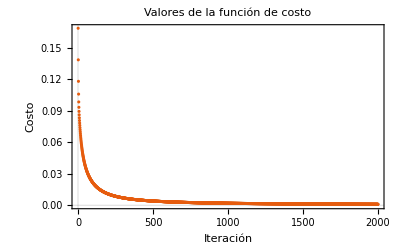

```mathematica
td = {{{0,0},{0}},{{0,1},{0}},{{1,0},{0}},{{1,1},{1}}}; (* Datos de entrenamiento. *)
Print["Datos de entrenamiento."];
Grid[td, Frame-> All]
feed = Table[i[[1]],{i,td}];
Initialize[{2,1}]; (* Se inicia una red neuronal de 2 neuronas en la capa de entrada y 1 en la de salida. *)
Print["Los resultados de la red sin entrenar son:"];
ShowResults[feed];
SGD[td,2000,4,3]; (* Se entrena la red con 2000 iteraciones, sets de 4 elementos y η = 3. *)
Print["Los resultados de la red entrenada son:"];
ShowResults[feed];
ShowInfo[]
```

La compuerta XOR es un poco más complicada, y necesita una red con una capa oculta. Si no se agrega esta capa oculta la red converge a dar 0.5 como resultado en todas las entradas.

Datos de entrenamiento.

{0,0} | {0}
{0,1} | {1}
{1,0} | {1}
{1,1} | {0}

Los resultados de la red sin entrenar son:

{0, 0} → {{0.624163}}

{0, 1} → {{0.628092}}

{1, 0} → {{0.645496}}

{1, 1} → {{0.64807}}

Los resultados de la red entrenada son:

{0, 0} → {{0.0418888}}

{0, 1} → {{0.962252}}

{1, 0} → {{0.962347}}

{1, 1} → {{0.04012}}

Información del resultado:

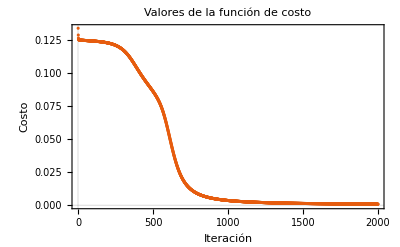

```mathematica
td = {{{0,0},{0}},{{0,1},{1}},{{1,0},{1}},{{1,1},{0}}}; (* Datos de entrenamiento. *)
Print["Datos de entrenamiento."];
Grid[td, Frame-> All]
feed = Table[i[[1]],{i,td}];
Initialize[{2,2,1}]; (* Se inicia una red neuronal de 2 neuronas en la capa de entrada, 2 en la capa oculta y 1 en la de salida. *)
Print["Los resultados de la red sin entrenar son:"];
ShowResults[feed];
SGD[td,2000,4,3]; (* Se entrena la red con 2000 iteraciones, sets de 4 elementos y η = 3. *)
Print["Los resultados de la red entrenada son:"];
ShowResults[feed];
ShowInfo[]
```

Aplicación: Determinar el idioma de un texto

El objetivo de esta aplicación es determinar el idioma de una cadena de texto. Cada idioma posee una distribución característica de la frecuencia de aparición de cada uno de sus caracteres. Aprovechando este tipo de distribución se puede entrenar una red neuronal.

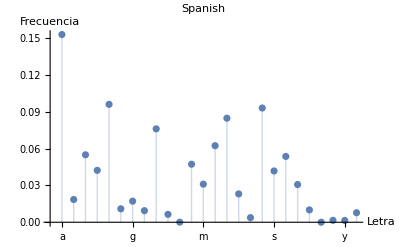

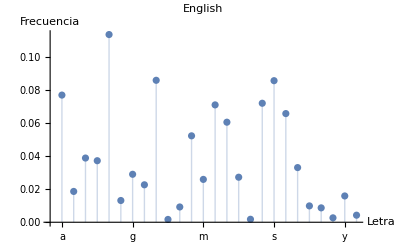

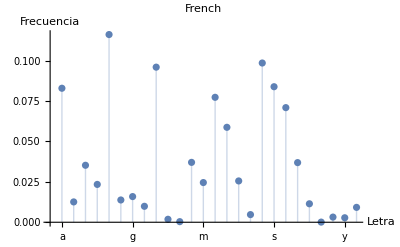

```mathematica
GenLangDist[lang_]:=Module[{joineddict,diclen,dictcounts,dictfrec},joineddict=StringJoin[DictionaryLookup[{lang,All}]];
diclen=StringLength[joineddict];
dictcounts=CharacterCounts[joineddict];
dictfrec=Table[dictcounts[[i]]/diclen,{i,Alphabet[]}];
ListPlot[dictfrec,Ticks->{Thread[{Table[i,{i,Length[CharacterRange["a","z"]]}],CharacterRange["a","z"]}],Automatic,{-1,1}},Filling->Axis,AxesLabel->{"Letra","Frecuencia"},BaseStyle->{FontSize->13},PlotLabel->lang]
];
GenLangDist["Spanish"]
GenLangDist["English"]
GenLangDist["French"]
```

El entrenamiento no se realizará sobre el diccionario debido a que el objetivo es clasificar un texto, y en los textos la distribución de frecuencia de caracteres es modificada por las palabras que se suelen repetir más comúnmente. Los datos de entrenamiento se generarán a partir de muestras de textos. El muestreo se realiza seleccionando partes aleatorias del texto y contando la frecuencia de aparición de cada caracter. Esto genera una lista de 26 elementos, donde cada una corresponde a la frecuencia de aparición de cada letra en orden alfabético. Los textos de entrenamiento disponibles están en los idiomas Español, Ingles, Francés y Alemán.

Test 1.

Se escogió una muestra aleatoria en: Spanish, y el resultado de la red al calcular su resultado es: Spanish

Test 2.

Pruebas superadas: 100 de 100.

Test 3.

Resultado de la clasificación: Spanish

Resultado de la clasificación: English

Información del resultado:

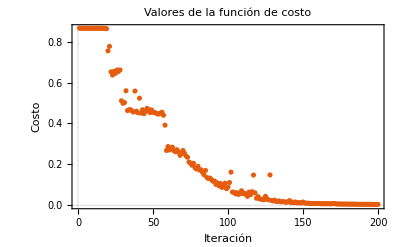

```mathematica
categoricalConvTable = {};
GetTrainingData[] := Module[{path, files, samplesize, samples, trainingdata,text,langname, del, len, samplepos, textsample,counts,dist,languages,basearray},
path = NotebookDirectory[] <> "TrainingData/";
SetDirectory[path];
files = FileNames[];
samplesize= 5000;
samples = 50;
trainingdata = {};

Do[
langname = FileBaseName[f];
text =Import[f];
text = ToLowerCase[text];
text = StringReplace[text,{"á"-> "a", "é" -> "e","í"-> "i", "ó" -> "o", "ú" -> "u", "ñ" -> "n", "ü" -> "u"}];
del = Complement[Keys[CharacterCounts[text]],Alphabet[]];
text = StringReplace[text,del-> ""];
len = StringLength[text];

(* Genera muestras y toma la distribución *)
Do[
samplepos = RandomInteger[{1,len-samplesize}];
textsample = StringTake[text,{samplepos,samplepos+samplesize}];
counts = CharacterCounts[textsample];
dist = Table[counts[[i]]/samplesize,{i, Alphabet[]}];
dist = {dist,langname};
dist = ReplaceAll[dist,Missing[_,_]->0];
AppendTo[trainingdata,dist];
,{samples}
];
,{f,files}
];

languages = DeleteDuplicates[trainingdata[[All,2]]];
basearray = ConstantArray[0,Length[languages]];
categoricalConvTable = Table[{languages[[i]], ReplacePart[basearray,i-> 1]},{i,1,Length[languages]}];
Return[trainingdata];
];

CategoricalToNumeric[td_] := Module[{data},
data = td;
Do[
data = ReplaceAll[data,categoricalConvTable[[i]][[1]] -> categoricalConvTable[[i]][[2]]];
,{i,1,Length[categoricalConvTable]}
];
Return[data];
];

NumericToCategorical[list_] := Module[{data,found},
data = list;
found = 0;
Do[
found += Count[{data},categoricalConvTable[[i]][[2]]];
,{i,1,Length[categoricalConvTable]}
];

If[found ≠ 0,
Do[
data = Replace[data,categoricalConvTable[[i]][[2]] -> categoricalConvTable[[i]][[1]]];
,{i,1,Length[categoricalConvTable]}
];
Return[data];,
Return["Clasificación erronea"];
]
];

GetDistFromText[text_]:=Module[{t,del,counts,dist,samplesize},
t = text;
t = ToLowerCase[t];
t=  StringReplace[t,{"á"-> "a", "é" -> "e","í"-> "i", "ó" -> "o", "ú" -> "u", "ñ" -> "n", "ü" -> "u"}];
del = Complement[Keys[CharacterCounts[t]],Alphabet[]];
t = StringReplace[t,del-> ""];
counts = CharacterCounts[t];
samplesize = StringLength[t];
dist = Table[counts[[i]]/samplesize,{i, Alphabet[]}];
dist = ReplaceAll[dist,Missing[_,_]->0];
Return[dist];
];

GetRandomTestData[] :=Module[{path, files, samplesize, samples, trainingdata, f,langname,text,del,len,samplepos,textsample,counts,dist},
path = NotebookDirectory[] <> "TrainingData/";
SetDirectory[path];
files = FileNames[];
samplesize= 5000;
samples = 50;
trainingdata = {};
f = RandomSample[files,1][[1]];

langname = FileBaseName[f];
text =Import[f];
text = ToLowerCase[text];
text = StringReplace[text,{"á"-> "a", "é" -> "e","í"-> "i", "ó" -> "o", "ú" -> "u", "ñ" -> "n", "ü" -> "u"}];
del = Complement[Keys[CharacterCounts[text]],Alphabet[]];
text = StringReplace[text,del-> ""];
len = StringLength[text];

samplepos = RandomInteger[{1,len-samplesize}];
textsample = StringTake[text,{samplepos,samplepos+samplesize}];
counts = CharacterCounts[textsample];
dist = Table[counts[[i]]/samplesize,{i, Alphabet[]}];
dist = {dist,CategoricalToNumeric[langname]};
dist = ReplaceAll[dist,Missing[_,_]->0];
Return[dist];
];

TestResult[td_] := Module[{sample},
sample = RandomSample[td,1][[1]];
Print["Se escogió una muestra aleatoria en: " <> NumericToCategorical[sample[[2]]] <>", y el resultado de la red al calcular su resultado es: " <> NumericToCategorical[Round[Flatten[FeedForward[sample[[1]]]]]]];
];

ScoreResults[td_,trials_:100]:= Module[{data,score},
score = 0;
Do[
data = GetRandomTestData[];
If[data[[2]] == Round[Flatten[FeedForward[data[[1]]]]], score++];
,{trials}
];
Print["Pruebas superadas: " <> ToString[score] <> " de " <> ToString[trials] <> "."];
];
ClassifyText[text_] := Module[{dist},
dist = GetDistFromText[text];
Print["Resultado de la clasificación: " <> NumericToCategorical[Round[Flatten[FeedForward[dist]]]]];
];

td =CategoricalToNumeric[GetTrainingData[]];
Initialize[{26,26,4}]; 
SGD[td,200,10,3];
Print["Test 1."];
TestResult[td];
Print["Test 2."];
ScoreResults[td];
Print["Test 3."];
ClassifyText["En el principio creó Dios los cielos y la tierra. Y la tierra estaba desordenada y vacía, y las tinieblas estaban sobre la faz del abismo, y el Espíritu de Dios se movía sobre la faz de las aguas. Y dijo Dios: Sea la luz; y fue la luz. Y vio Dios que la luz era buena; y separó Dios la luz de las tinieblas. Y llamó Dios a la luz Día, y a las tinieblas llamó Noche. Y fue la tarde y la mañana un día."]

ClassifyText["In the beginning God created the heaven and the earth. And the earth was waste and void; and darkness was upon the face of the deep: and the spirit of God moved upon the face of the waters. And God said, Let there be light: and there was light. And God saw the light, that it was good: and God divided the light from the darkness. And God called the light Day, and the darkness he called Night. And there was evening and there was morning, one day."]
ShowInfo[]
```

Aplicación: Clasificar dígitos

```mathematica
DigitToOutput[index_]:= Module[{out},
out = ConstantArray[0,{10}];
out[[index+1]] = 1;
Return[out];
];

OutputToDigit[out_]:= Module[{},
pos = Position[out,1];
If[Length[pos] == 1,
Return[pos[[1]][[1]]-1];,
Return["Clasificación erronea"];
]
];

td=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
td = Table[{Flatten[ImageData[td[[i]][[1]]]],DigitToOutput[td[[i]][[2]]]},{i,1,Length[td]}];
```

```mathematica
sampletd=RandomChoice[td,{200}];
Initialize[{784,30,10}]; 
SGD[td,20,10,3];
OutputToDigit[sampletd[[10]][[2]]]
Round[FeedForward[sampletd[[10]][[1]]]]
```

$Aborted